```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 10.2.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../UFOandFAModels/UV_BSM_ToyModel_ren-FA/UV_BSM_ToyModel_ren-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## u u → t t (1-loop)

generic model {Lorentz} initialized

classes model {../../UFOandFAModels/UV_BSM_ToyModel_ren-FA/UV_BSM_ToyModel_ren-FA} initialized

in total: 2 Particles insertions

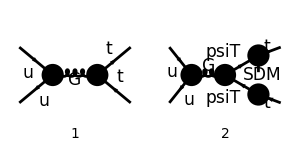

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { F[7],-F[7]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 300,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True,SheetHeader->None];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[DiracSimplify[ampA]]
```

in total: 2 Particles amplitudes

1/(p1+p2)^2 gs^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((2 yDM^2 (φ(-k2)).(γ·q).(φ(k1)) (φ(p1,MT)).(γ·q).(γ̄)^6.(φ(-p2,MT)))/((q^2-mSDM^2).((p1+q)^2-mPsiT^2).((p2-q)^2-mPsiT^2))+(φ(-k2)).γ^Lor2.(φ(k1)) ((φ(p1,MT)).γ^Lor2.(γ̄)^6.(φ(-p2,MT)) ((yDM^2 (mPsiT^2-q^2))/((q^2-mSDM^2).((p1+q)^2-mPsiT^2).((p2-q)^2-mPsiT^2))-ⅈ (2 π^2 deltaCTR yDM^2+1))+(MT yDM^2 (MT (φ(p1,MT)).γ^Lor2.(γ̄)^7.(φ(-p2,MT))+(φ(p1,MT)).γ^Lor2.(γ·q).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ·q).γ^Lor2.(γ̄)^7.(φ(-p2,MT))))/((q^2-mSDM^2).((p1+q)^2-mPsiT^2).((p2-q)^2-mPsiT^2))-ⅈ (2 π^2 deltaCTL yDM^2+1) (φ(p1,MT)).γ^Lor2.(γ̄)^7.(φ(-p2,MT))))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify)/.{LorentzIndex[a_,D]->LorentzIndex[μ,D]}
```

-1/(p1+p2)^2 ⅈ gs^2 (π^2 B_0(p1^2+2 (p1·p2)+p2^2,mPsiT^2,mPsiT^2) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) yDM^2-π^2 C_0(p1^2,p2^2,p1^2+2 (p1·p2)+p2^2,mPsiT^2,mSDM^2,mPsiT^2) (φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)) MT^2+(mPsiT^2-mSDM^2) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))) yDM^2-MT π^2 (φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ·p1).γ^μ.(γ̄)^7.(φ(-p2,MT))) C_1(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2) yDM^2+MT π^2 (φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ·p2).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ·p2).γ^μ.(γ̄)^7.(φ(-p2,MT))) C_1(p2^2,p1^2+2 (p1·p2)+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2) yDM^2-2 π^2 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) C_00(p1^2,p2^2,p1^2+2 (p1·p2)+p2^2,mPsiT^2,mSDM^2,mPsiT^2) yDM^2-2 π^2 (φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT)) C_11(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2) yDM^2-2 π^2 (φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)) C_11(p2^2,p1^2+2 (p1·p2)+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2) yDM^2+2 π^2 ((φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))) C_12(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2) yDM^2+(φ(-k2)).γ^μ.(φ(k1)) (2 deltaCTR π^2 (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) yDM^2+2 deltaCTL π^2 (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)) yDM^2+(φ(p1,MT)).γ^μ.((γ̄)^6+(γ̄)^7).(φ(-p2,MT)))) T_Col2Col1^Glu5 T_Col3Col4^Glu5

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}] 
ampD=Simplify[ampC-ampSM]
```

-(ⅈ gs^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.((γ̄)^6+(γ̄)^7).(φ(-p2,MT)))/(p1+p2)^2

1/(p1+p2)^2 ⅈ π^2 gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) (-(φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) (B_0(s,mPsiT^2,mPsiT^2)+(mSDM^2-mPsiT^2) C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+2 (deltaCTR-C_00(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)))+(MT^2 C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)-2 deltaCTL) (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT))+MT C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) ((φ(p1,MT)).γ^μ.(γ·p1).(γ̄)^6.(φ(-p2,MT))-(φ(p1,MT)).γ^μ.(γ·p2).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ·p1).γ^μ.(γ̄)^7.(φ(-p2,MT))-(φ(p1,MT)).(γ·p2).γ^μ.(γ̄)^7.(φ(-p2,MT))))+2 ((φ(-k2)).(γ·p2).(φ(k1)) (C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))-C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT)))+(φ(-k2)).(γ·p1).(φ(k1)) (C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))-C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)))))

```mathematica
Cases2[ampD,{A0,B0,C0,D0,PaVe}]
```

{B_0(p1^2+2 (p1·p2)+p2^2,mPsiT^2,mPsiT^2),C_0(p1^2,p2^2,p1^2+2 (p1·p2)+p2^2,mPsiT^2,mSDM^2,mPsiT^2),C_1(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2),C_1(p2^2,2 (p1·p2)+p1^2+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2),C_00(p1^2,p2^2,2 (p1·p2)+p1^2+p2^2,mPsiT^2,mSDM^2,mPsiT^2),C_11(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2),C_11(p2^2,2 (p1·p2)+p1^2+p2^2,p1^2,mSDM^2,mPsiT^2,mPsiT^2),C_12(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mSDM^2,mPsiT^2,mPsiT^2)}

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampE = Expand[Collect[Simplify[(  ampD)/.aS->GS^2/(4 Pi),Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},FullSimplify]] ;
```

1/(p1+p2)^2 ⅈ π^2 gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) (-(φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) (B_0(s,mPsiT^2,mPsiT^2)+(mSDM^2-mPsiT^2) C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+2 (deltaCTR-C_00(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)))+(MT^2 C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)-2 deltaCTL) (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT))+MT C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) ((φ(p1,MT)).γ^μ.(γ·p1).(γ̄)^6.(φ(-p2,MT))-(φ(p1,MT)).γ^μ.(γ·p2).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ·p1).γ^μ.(γ̄)^7.(φ(-p2,MT))-(φ(p1,MT)).(γ·p2).γ^μ.(γ̄)^7.(φ(-p2,MT))))+2 ((φ(-k2)).(γ·p2).(φ(k1)) (C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))-C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT)))+(φ(-k2)).(γ·p1).(φ(k1)) (C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))-C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)))))

```mathematica
FullSimplify[DiracSimplify[ampE//.{PaVe[0,0,__]->C00,PaVe[1,1,__]->C11,PaVe[1,2,__]->C12,PaVe[1,__]->C1,B0[__]->B0,C0[__]->C0,Subscript[B,0][__]->B0,Subscript[C,0][__]->C0}]]/.{(DiracGamma[7]->1-DiracGamma[6])}/.{mSDM->mPsiT}
```

-1/(p1+p2)^2 ⅈ π^2 gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) ((B0-2 C00+2 C1 MT^2+2 deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(2 deltaCTL-MT^2 (C0+2 C1)) (φ(p1,MT)).γ^μ.(1-(γ̄)^6).(φ(-p2,MT)))-2 MT (φ(-k2)).(γ·p1).(φ(k1)) ((C1+C11) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+C12 (φ(p1,MT)).(1-(γ̄)^6).(φ(-p2,MT)))+2 MT (φ(-k2)).(γ·p2).(φ(k1)) ((C1+C11) (φ(p1,MT)).(1-(γ̄)^6).(φ(-p2,MT))+C12 (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))))

```mathematica
ampEsimp2=FullSimplify[DotSimplify[DiracSimplify[ampE]]]/.{(DiracGamma[7]->1-DiracGamma[6])}
```

-1/(p1+p2)^2 ⅈ π^2 gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) (B_0(s,mPsiT^2,mPsiT^2)+(mSDM^2-mPsiT^2) C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+2 (-C_00(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+MT^2 C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+deltaCTR))+(2 deltaCTL-MT^2 (C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+2 C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2))) (φ(p1,MT)).γ^μ.(1-(γ̄)^6).(φ(-p2,MT)))+2 MT ((C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)) ((φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(1-(γ̄)^6).(φ(-p2,MT))-(φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)))+C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) ((φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))-(φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(1-(γ̄)^6).(φ(-p2,MT)))))

```mathematica
sps=Cases2[ampEsimp2,Spinor]
moms=Cases2[ampEsimp2,DiracGamma]
```

{φ(k1),φ(-k2),φ(p1,MT),φ(-p2,MT)}

{(γ̄)^6,γ^μ,γ·p1,γ·p2}

```mathematica
(* phi(k1).p1slash.phi(-k2) + phi(k1).p2slash.phi(-k2) = phi(k1).(p1slash+p2slash).phi(-k2) = phi(k1).(k1slash+k2slash).phi(-k2) = 0 *)
ampEsimp3=Collect[ampEsimp2,{sps[[3]].moms[[1]].sps[[4]]},Simplify]/.{sps[[2]].moms[[3]].sps[[1]]+sps[[2]].moms[[4]].sps[[1]]->0};
```

```mathematica
ampEsimp4=FullSimplify[DiracSimplify[DiracSimplify[ampEsimp3]/.(DiracGamma[7]->1-DiracGamma[6])]];
```

```mathematica
ampF=Collect[ampEsimp4,{sps[[2]].moms[[2]].sps[[1]],sps[[3]].moms[[2]].DiracGamma[6].sps[[4]],sps[[3]].moms[[2]].sps[[4]],sps[[2]].moms[[3]].sps[[1]],sps[[2]].moms[[4]].sps[[1]]},FullSimplify]/.{MT->0, mSDM->mPsiT, deltaCTL->0, deltaCTR->0}
```

-(ⅈ π^2 gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (B_0(s,mPsiT^2,mPsiT^2)-2 C_00(0,0,s,mPsiT^2,mPsiT^2,mPsiT^2)) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1)).γ^μ.(γ̄)^6.(φ(-p2)))/(p1+p2)^2

```mathematica
loopFuncs = Cases[ampF,_B0|_C0|_PaVe,Infinity]//DeleteDuplicates
loopFuncsampF=Table[FullSimplify[PaXEvaluate[loopFuncs[[i]],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{mSDM,mPsiT,0}}]/.{EulerGamma->0,ScaleMu->mPsiT/(√(4 Pi))}],{i,1,Length[loopFuncs]}]
loopSubs = Table[loopFuncs[[i]]-> loopFuncsampF[[i]],{i,1,Length[loopFuncs]}];
ampG=Collect[Simplify[ ampF/.{deltaCTL->0,deltaCTR->0,MT->0}/.loopSubs],{Epsilon,s,mPsiT,Log[a_],deltaCTL,deltaCTR},Simplify]
ampG = FullSimplify[ampG];
```

{B_0(s,mPsiT^2,mPsiT^2),C_00(0,0,s,mPsiT^2,mPsiT^2,mPsiT^2)}

{(ε √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 ε s+s)/(16 π^4 ε s),(ε log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)) (√(s (s-4 mPsiT^2))+mPsiT^2 log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)))+3 ε s+s)/(64 π^4 ε s)}

((ⅈ gs^2 mPsiT^2 yDM^2 log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1)).γ^μ.(γ̄)^6.(φ(-p2)))/(32 π^2 (p1+p2)^2)-(ⅈ gs^2 yDM^2 √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1)).γ^μ.(γ̄)^6.(φ(-p2)))/(32 π^2 (p1+p2)^2))/s+-(ⅈ gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1)).γ^μ.(γ̄)^6.(φ(-p2)))/(32 π^2 ε (p1+p2)^2)-(ⅈ gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1)).γ^μ.(γ̄)^6.(φ(-p2)))/(32 π^2 (p1+p2)^2)

```mathematica
ampH = Collect[ampG/.{Log[(√(s(s-4 mPsiT^2))+2 mPsiT^2 -s)/(2 mPsiT^2)]->L[s,mPsiT],√(s(s-4 mPsiT^2))->Δ[s,mPsiT]},{Epsilon},FullSimplify]/.{mSDM-> mPsiT};
ampH/.{MT->0}
```

-(ⅈ gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1)).γ^μ.(γ̄)^6.(φ(-p2)))/(32 π^2 ε (p1+p2)^2)-(ⅈ gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (L(s,mPsiT) (Δ(s,mPsiT)-mPsiT^2 L(s,mPsiT))+s) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1)).γ^μ.(γ̄)^6.(φ(-p2)))/(32 π^2 s (p1+p2)^2)

```mathematica
FCSetDiracGammaScheme["NDR"]
ampInterference=ampSM*RealClean[ComplexConjugate[ampH]]+RealClean[ComplexConjugate[ampSM]]*ampH // DiracSimplify;


ampSummed=FermionSpinSum[ampInterference //SUNSimplify]//DiracSimplify;

(*1. Force the Scheme to NDR (Standard 4D)*)FCSetDiracGammaScheme["NDR"];

(*2. Define Kinematics*)
ruleKinematics={SPD[k1,k2]->s/2,SPD[p1,p2]->s/2-MT^2,SPD[k1,k1]->0,SPD[k2,k2]->0,SPD[p1,p1]->MT^2,SPD[p2,p2]->MT^2};

(*3. The Nuclear Option:Replace'tr' with'TR'*)
(*We look for the head'DiracTrace' (which displays as'tr') and force it to'TR'*)

forceCalc=ampSummed//(*Step A:Convert everything to 4 Dimensions first to be safe*)ChangeDimension[#,4]&//(*Step B:Replace the inert trace head with the active one*)ReplaceAll[#,DiracTrace[x_]:>TR[x]]&//(*Step C:Just in case it's a raw symbol'tr'*)ReplaceAll[#,tr[x_]:>TR[x]]&//(*Step D:Simplify using Kinematics*)ReplaceAll[#,ruleKinematics]&//Simplify;

(*4. Display*)
Print["Calculated Trace:"];
Collect[forceCalc/.{D->4},{Epsilon}, FullSimplify]
```

NDR

Calculated Trace:

1/(4 π^2 s^2)gs^4 (C_A^2-1) (1/(OverBar[p1]+OverBar[p2])^2)^2 ((OverBar[k1]·OverBar[p2]) ((OverBar[k2]·OverBar[p1]) (s (yDM^2 (s-6 MT^2)+64 π^2 s)-yDM^2 L(s,mPsiT) ((mPsiT^2 (2 MT^2+s)+MT^2 s) L(s,mPsiT)+(2 MT^2-s) Δ(s,mPsiT)))+2 MT^2 yDM^2 (OverBar[k2]·OverBar[p2]) (L(s,mPsiT) (mPsiT^2 L(s,mPsiT)+Δ(s,mPsiT))+3 s))+(OverBar[k1]·OverBar[p1]) (2 MT^2 yDM^2 (OverBar[k2]·OverBar[p1]) (L(s,mPsiT) (mPsiT^2 L(s,mPsiT)+Δ(s,mPsiT))+3 s)+(OverBar[k2]·OverBar[p2]) (s (yDM^2 (s-6 MT^2)+64 π^2 s)-yDM^2 L(s,mPsiT) ((mPsiT^2 (2 MT^2+s)+MT^2 s) L(s,mPsiT)+(2 MT^2-s) Δ(s,mPsiT))))+MT^2 (-(OverBar[k1]·OverBar[k2])) (yDM^2 L(s,mPsiT) (MT^2 (4 mPsiT^2+s) L(s,mPsiT)+2 (2 MT^2-s) Δ(s,mPsiT))-4 s (yDM^2 (s-3 MT^2)+16 π^2 s)))+(gs^4 yDM^2 (C_A^2-1) (1/(OverBar[p1]+OverBar[p2])^2)^2 (MT^2 (OverBar[k1]·OverBar[k2])+(OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])+(OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2])))/(4 π^2 ε)

Interference Term (Finite, 4D Limit):

1/(16 ε π^2 s)C_A C_F gs^4 (1/(OverBar[p1]+OverBar[p2])^2)^2 (-ε mPsiT^2 (φ(-OverBar[p2],MT)).(γ̄·OverBar[k2]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k1]).(γ̄)^6.(φ(-OverBar[p2])) (L(s,mPsiT))^2 yDM^2-ε mPsiT^2 (φ(-OverBar[p2],MT)).(γ̄·OverBar[k1]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k2]).(γ̄)^6.(φ(-OverBar[p2])) (L(s,mPsiT))^2 yDM^2+ε s (φ(-OverBar[p2],MT)).(γ̄·OverBar[k2]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k1]).(γ̄)^6.(φ(-OverBar[p2])) yDM^2+s (φ(-OverBar[p2],MT)).(γ̄·OverBar[k2]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k1]).(γ̄)^6.(φ(-OverBar[p2])) yDM^2+ε s (φ(-OverBar[p2],MT)).(γ̄·OverBar[k1]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k2]).(γ̄)^6.(φ(-OverBar[p2])) yDM^2+s (φ(-OverBar[p2],MT)).(γ̄·OverBar[k1]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k2]).(γ̄)^6.(φ(-OverBar[p2])) yDM^2+ε mPsiT^2 (φ(-OverBar[p2],MT)).(γ̄)^μ.(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄)^μ.(γ̄)^6.(φ(-OverBar[p2])) (L(s,mPsiT))^2 (OverBar[k1]·OverBar[k2]) yDM^2+ε mPsiT^2 (φ(OverBar[p1],MT)).(γ̄)^($AL($3111)).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄)^($AL($3111)).(γ̄)^6.(φ(OverBar[p1])) (L(s,mPsiT))^2 (OverBar[k1]·OverBar[k2]) yDM^2-ε s (φ(-OverBar[p2],MT)).(γ̄)^μ.(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄)^μ.(γ̄)^6.(φ(-OverBar[p2])) (OverBar[k1]·OverBar[k2]) yDM^2-s (φ(-OverBar[p2],MT)).(γ̄)^μ.(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄)^μ.(γ̄)^6.(φ(-OverBar[p2])) (OverBar[k1]·OverBar[k2]) yDM^2-ε s (φ(OverBar[p1],MT)).(γ̄)^($AL($3111)).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄)^($AL($3111)).(γ̄)^6.(φ(OverBar[p1])) (OverBar[k1]·OverBar[k2]) yDM^2-s (φ(OverBar[p1],MT)).(γ̄)^($AL($3111)).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄)^($AL($3111)).(γ̄)^6.(φ(OverBar[p1])) (OverBar[k1]·OverBar[k2]) yDM^2+ε (φ(-OverBar[p2],MT)).(γ̄·OverBar[k2]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k1]).(γ̄)^6.(φ(-OverBar[p2])) L(s,mPsiT) Δ(s,mPsiT) yDM^2+ε (φ(-OverBar[p2],MT)).(γ̄·OverBar[k1]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k2]).(γ̄)^6.(φ(-OverBar[p2])) L(s,mPsiT) Δ(s,mPsiT) yDM^2-ε (φ(-OverBar[p2],MT)).(γ̄)^μ.(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄)^μ.(γ̄)^6.(φ(-OverBar[p2])) L(s,mPsiT) (OverBar[k1]·OverBar[k2]) Δ(s,mPsiT) yDM^2-ε (φ(OverBar[p1],MT)).(γ̄)^($AL($3111)).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄)^($AL($3111)).(γ̄)^6.(φ(OverBar[p1])) L(s,mPsiT) (OverBar[k1]·OverBar[k2]) Δ(s,mPsiT) yDM^2+32 ε π^2 s (φ(OverBar[p1])).(γ̄·OverBar[k2]).(φ(-OverBar[p2])) (φ(-OverBar[p2],MT)).(γ̄·OverBar[k1]).(φ(OverBar[p1],MT))+32 ε π^2 s (φ(OverBar[p1])).(γ̄·OverBar[k1]).(φ(-OverBar[p2])) (φ(-OverBar[p2],MT)).(γ̄·OverBar[k2]).(φ(OverBar[p1],MT))-32 ε π^2 s (φ(OverBar[p1],MT)).(γ̄)^($AL($3111)).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄)^($AL($3111)).(φ(OverBar[p1])) (OverBar[k1]·OverBar[k2])-32 ε π^2 s (φ(OverBar[p1])).(γ̄)^($AL($3113)).(φ(-OverBar[p2])) (φ(-OverBar[p2],MT)).(γ̄)^($AL($3113)).(φ(OverBar[p1],MT)) (OverBar[k1]·OverBar[k2])+(φ(OverBar[p1],MT)).(γ̄·OverBar[k2]).(φ(-OverBar[p2],MT)) ((φ(-OverBar[p2])).(γ̄·OverBar[k1]).(γ̄)^6.(φ(OverBar[p1])) (-ε mPsiT^2 (L(s,mPsiT))^2+ε Δ(s,mPsiT) L(s,mPsiT)+ε s+s) yDM^2+32 ε π^2 s (φ(-OverBar[p2])).(γ̄·OverBar[k1]).(φ(OverBar[p1])))+(φ(OverBar[p1],MT)).(γ̄·OverBar[k1]).(φ(-OverBar[p2],MT)) ((φ(-OverBar[p2])).(γ̄·OverBar[k2]).(γ̄)^6.(φ(OverBar[p1])) (-ε mPsiT^2 (L(s,mPsiT))^2+ε Δ(s,mPsiT) L(s,mPsiT)+ε s+s) yDM^2+32 ε π^2 s (φ(-OverBar[p2])).(γ̄·OverBar[k2]).(φ(OverBar[p1]))))

1/(16 ε π^2)C_A C_F (1/(OverBar[p1]+OverBar[p2])^2)^2 ((φ(-OverBar[p2],MT)).(γ̄·OverBar[k2]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k1]).(γ̄)^6.(φ(-OverBar[p2])) yDM^2+(φ(-OverBar[p2],MT)).(γ̄·OverBar[k1]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k2]).(γ̄)^6.(φ(-OverBar[p2])) yDM^2+(φ(OverBar[p1],MT)).(γ̄·OverBar[k2]).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄·OverBar[k1]).(γ̄)^6.(φ(OverBar[p1])) yDM^2+(φ(OverBar[p1],MT)).(γ̄·OverBar[k1]).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄·OverBar[k2]).(γ̄)^6.(φ(OverBar[p1])) yDM^2-(φ(-OverBar[p2],MT)).(γ̄)^μ.(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄)^μ.(γ̄)^6.(φ(-OverBar[p2])) (OverBar[k1]·OverBar[k2]) yDM^2-(φ(OverBar[p1],MT)).(γ̄)^($AL($3111)).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄)^($AL($3111)).(γ̄)^6.(φ(OverBar[p1])) (OverBar[k1]·OverBar[k2]) yDM^2) gs^4+1/(16 π^2 s)C_A C_F (1/(OverBar[p1]+OverBar[p2])^2)^2 (-mPsiT^2 (φ(-OverBar[p2],MT)).(γ̄·OverBar[k2]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k1]).(γ̄)^6.(φ(-OverBar[p2])) (L(s,mPsiT))^2 yDM^2-mPsiT^2 (φ(-OverBar[p2],MT)).(γ̄·OverBar[k1]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k2]).(γ̄)^6.(φ(-OverBar[p2])) (L(s,mPsiT))^2 yDM^2+s (φ(-OverBar[p2],MT)).(γ̄·OverBar[k2]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k1]).(γ̄)^6.(φ(-OverBar[p2])) yDM^2+s (φ(-OverBar[p2],MT)).(γ̄·OverBar[k1]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k2]).(γ̄)^6.(φ(-OverBar[p2])) yDM^2+mPsiT^2 (φ(-OverBar[p2],MT)).(γ̄)^μ.(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄)^μ.(γ̄)^6.(φ(-OverBar[p2])) (L(s,mPsiT))^2 (OverBar[k1]·OverBar[k2]) yDM^2+mPsiT^2 (φ(OverBar[p1],MT)).(γ̄)^($AL($3111)).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄)^($AL($3111)).(γ̄)^6.(φ(OverBar[p1])) (L(s,mPsiT))^2 (OverBar[k1]·OverBar[k2]) yDM^2-s (φ(-OverBar[p2],MT)).(γ̄)^μ.(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄)^μ.(γ̄)^6.(φ(-OverBar[p2])) (OverBar[k1]·OverBar[k2]) yDM^2-s (φ(OverBar[p1],MT)).(γ̄)^($AL($3111)).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄)^($AL($3111)).(γ̄)^6.(φ(OverBar[p1])) (OverBar[k1]·OverBar[k2]) yDM^2+(φ(-OverBar[p2],MT)).(γ̄·OverBar[k2]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k1]).(γ̄)^6.(φ(-OverBar[p2])) L(s,mPsiT) Δ(s,mPsiT) yDM^2+(φ(-OverBar[p2],MT)).(γ̄·OverBar[k1]).(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄·OverBar[k2]).(γ̄)^6.(φ(-OverBar[p2])) L(s,mPsiT) Δ(s,mPsiT) yDM^2-(φ(-OverBar[p2],MT)).(γ̄)^μ.(φ(OverBar[p1],MT)) (φ(OverBar[p1])).(γ̄)^μ.(γ̄)^6.(φ(-OverBar[p2])) L(s,mPsiT) (OverBar[k1]·OverBar[k2]) Δ(s,mPsiT) yDM^2-(φ(OverBar[p1],MT)).(γ̄)^($AL($3111)).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄)^($AL($3111)).(γ̄)^6.(φ(OverBar[p1])) L(s,mPsiT) (OverBar[k1]·OverBar[k2]) Δ(s,mPsiT) yDM^2+32 π^2 s (φ(OverBar[p1])).(γ̄·OverBar[k2]).(φ(-OverBar[p2])) (φ(-OverBar[p2],MT)).(γ̄·OverBar[k1]).(φ(OverBar[p1],MT))+32 π^2 s (φ(OverBar[p1])).(γ̄·OverBar[k1]).(φ(-OverBar[p2])) (φ(-OverBar[p2],MT)).(γ̄·OverBar[k2]).(φ(OverBar[p1],MT))-32 π^2 s (φ(OverBar[p1],MT)).(γ̄)^($AL($3111)).(φ(-OverBar[p2],MT)) (φ(-OverBar[p2])).(γ̄)^($AL($3111)).(φ(OverBar[p1])) (OverBar[k1]·OverBar[k2])-32 π^2 s (φ(OverBar[p1])).(γ̄)^($AL($3113)).(φ(-OverBar[p2])) (φ(-OverBar[p2],MT)).(γ̄)^($AL($3113)).(φ(OverBar[p1],MT)) (OverBar[k1]·OverBar[k2])+(φ(OverBar[p1],MT)).(γ̄·OverBar[k2]).(φ(-OverBar[p2],MT)) ((φ(-OverBar[p2])).(γ̄·OverBar[k1]).(γ̄)^6.(φ(OverBar[p1])) (-mPsiT^2 (L(s,mPsiT))^2+Δ(s,mPsiT) L(s,mPsiT)+s) yDM^2+32 π^2 s (φ(-OverBar[p2])).(γ̄·OverBar[k1]).(φ(OverBar[p1])))+(φ(OverBar[p1],MT)).(γ̄·OverBar[k1]).(φ(-OverBar[p2],MT)) ((φ(-OverBar[p2])).(γ̄·OverBar[k2]).(γ̄)^6.(φ(OverBar[p1])) (-mPsiT^2 (L(s,mPsiT))^2+Δ(s,mPsiT) L(s,mPsiT)+s) yDM^2+32 π^2 s (φ(-OverBar[p2])).(γ̄·OverBar[k2]).(φ(OverBar[p1])))) gs^4

```mathematica
ampScalar =-((I*gs^2*yDM^2*SUNT[Glu5,Col2,Col1]*SUNT[Glu5,Col3,Col4]*(SpinorVBar[k2].GAD[mu].SpinorU[k1])*(SpinorUBar[p1,MT].GAD[mu].GA[6].SpinorV[p2,MT]))/(32*Pi^2*Epsilon*SPD[p1+p2]))

-(I*gs^2*SUNT[Glu5,Col2,Col1]*SUNT[Glu5,Col3,Col4]*(SpinorVBar[k2].GAD[mu].SpinorU[k1])*((yDM^2*(L[s,mST]*(mST^2*L[s,mST]+Delta[s,mST])+3*s)*(SpinorUBar[p1,MT].GAD[mu].GA[6].SpinorV[p2,MT]))+32*Pi^2*s*(SpinorUBar[p1,MT].GAD[mu].SpinorV[p2,MT])))/(32*Pi^2*s*SPD[p1+p2]);
```

-(ⅈ gs^2 yDM^2 T^Glu5.T^Col2.T^Col1 T^Glu5.T^Col3.T^Col4 v̄(k2).γ^mu.u(k1) ū(p1,MT).γ^mu.(γ̄)^6.v(p2,MT))/(32 π^2 ε (p1+p2)^2)

```mathematica
(*1. Define the Color Factor*)colorFac=SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]];

(*2. Define the exact Spinor Chains using CurlyPhi*)
(*Note:I am using Square Brackets[] which is the required syntax for functions in Mathematica*)

(*Light Current:phi(-k2).gamma.phi(k1)*)
Jlight=CurlyPhi[-k2].GAD[mu].CurlyPhi[k1];

(*Heavy Current (Right-Handed):phi(p1).gamma.P_R.phi(-p2)*)
JheavyR=CurlyPhi[p1].GAD[mu].GA[6].CurlyPhi[-p2];

(*Heavy Current (Vector):phi(p1).gamma.phi(-p2)*)
JheavyV=CurlyPhi[p1].GAD[mu].CurlyPhi[-p2];

(*3. Assemble the Expression*)
myExpr=(*First Term*)-((I*gs^2*yDM^2*colorFac*Jlight*JheavyR)/(32*Pi^2*Epsilon*SPD[p1+p2]))

(*Second Term*)
-((I*gs^2*colorFac*Jlight*(yDM^2*(L[s,mST]*(mST^2*L[s,mST]+Delta[s,mST])+3*s)*JheavyR+32*Pi^2*s*JheavyV))/(32*Pi^2*s*SPD[p1+p2]))
```

-(ⅈ gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 CurlyPhi(-k2).γ^mu.CurlyPhi(k1) CurlyPhi(p1).γ^mu.(γ̄)^6.CurlyPhi(-p2))/(32 π^2 ε (p1+p2)^2)

-1/(32 π^2 s (p1+p2)^2)ⅈ gs^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 CurlyPhi(-k2).γ^mu.CurlyPhi(k1) (yDM^2 (L(s,mST) (Delta(s,mST)+mST^2 L(s,mST))+3 s) CurlyPhi(p1).γ^mu.(γ̄)^6.CurlyPhi(-p2)+32 π^2 s CurlyPhi(p1).γ^mu.CurlyPhi(-p2))

```mathematica
SubsPV={(*---Tensor Coefficients---*)C00->PaXEvaluate[PaVe[0,0,{MT^2,s,MT^2},{mSDM^2,mPsiT^2,mPsiT^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/. {EulerGamma->0,ScaleMu->mPsiT/Sqrt[4 Pi]},C11->PaXEvaluate[PaVe[1,1,{MT^2,s,MT^2},{mSDM^2,mPsiT^2,mPsiT^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/. {EulerGamma->0,ScaleMu->mPsiT/Sqrt[4 Pi]},C12->PaXEvaluate[PaVe[1,2,{MT^2,s,MT^2},{mSDM^2,mPsiT^2,mPsiT^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/. {EulerGamma->0,ScaleMu->mPsiT/Sqrt[4 Pi]},C1->PaXEvaluate[PaVe[1,{MT^2,s,MT^2},{mSDM^2,mPsiT^2,mPsiT^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/. {EulerGamma->0,ScaleMu->mPsiT/Sqrt[4 Pi]},(*---Scalar C0 (Triangle)---*)(*Matches the arguments of C1,but with index 0*)C0->PaXEvaluate[PaVe[0,{MT^2,s,MT^2},{mSDM^2,mPsiT^2,mPsiT^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/. {EulerGamma->0,ScaleMu->mPsiT/Sqrt[4 Pi]},(*---Scalar B0 (Bubble)---*)(*Based on your previous output:B0(s,mPsiT^2,mPsiT^2)*)B0->PaXEvaluate[PaVe[0,{s},{mPsiT^2,mPsiT^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{s,0,1}}]/. {EulerGamma->0,ScaleMu->mPsiT/Sqrt[4 Pi]}};
```

### Coefficients for each term

```mathematica
factor=FeynAmpDenominator[PropagatorDenominator[Momentum[p1,D]+Momentum[p2,D],0]]SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]]
(*Define the Chains using YOUR notation*)(*sps[[1]]=u(k1),sps[[2]]=vBar(k2)*)(*sps[[3]]=uBar(p1),sps[[4]]=v(p2)*)(*moms[[2]]=gamma^mu (or similar vector)*)(*moms[[3]]=p1 slash,moms[[4]]=p2 slash*)chainVV=factor*(sps[[2]].moms[[2]].sps[[1]])*(sps[[3]].moms[[2]].sps[[4]]);

chainVR=factor*(sps[[2]].moms[[2]].sps[[1]])*(sps[[3]].moms[[2]].DiracGamma[6].sps[[4]]);

chainP1=factor*(sps[[2]].moms[[3]].sps[[1]])*(sps[[3]].sps[[4]]);

chainP2=factor*(sps[[2]].moms[[4]].sps[[1]])*(sps[[3]].sps[[4]]);

(*Now use these chains to extract coefficients*)
(*Note:Using'Coefficient' with these complex objects might still be fragile if ordering differs.*)
(*Dividing out the chain is safer.*)

(*Option A:Direct Coefficient (if ordering is identical)*)
CVV=Coefficient[ampF,chainVV];
CVR=Coefficient[ampF,chainVR];
CP1=Coefficient[ampF,chainP1];
CP2=Coefficient[ampF,chainP2];

(*Option B:Robust Select& Divide (Recommended)*)
(*We look for terms matching the'distinctive' part of the chain*)

(*Distinctive feature for VV:Contains moms[[2]] twice,NO DiracGamma[6]*)
termVV=Select[If[Head[ampF]===Plus,List@@ampF,{ampF}],(!FreeQ[#,moms[[2]]]&&FreeQ[#,DiracGamma[6]])&];
CVVRobust=Total[termVV]/chainVV//Simplify;

(*Distinctive feature for VR:Contains moms[[2]] twice AND DiracGamma[6]*)
termVR=Select[If[Head[ampF]===Plus,List@@ampF,{ampF}],(!FreeQ[#,moms[[2]]]&&!FreeQ[#,DiracGamma[6]])&];
CVRRobust=Total[termVR]/chainVR//Simplify;

(*Distinctive feature for P1:Contains moms[[3]]*)
termP1=Select[If[Head[ampF]===Plus,List@@ampF,{ampF}],!FreeQ[#,moms[[3]]]&];
CP1Robust=Total[termP1]/chainP1//Simplify;

(*Distinctive feature for P2:Contains moms[[4]]*)
termP2=Select[If[Head[ampF]===Plus,List@@ampF,{ampF}],!FreeQ[#,moms[[4]]]&];
CP2Robust=Total[termP2]/chainP2//Simplify;

Coeffs={CVVRobust,CVRRobust,CP1Robust,CP2Robust};
Print[Coeffs];
```

(T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2

{0,-(ⅈ gs^2 (π^2 yDM^2 (B0+C0 (mSDM^2-mPsiT^2)-2 C00) (φ(p1)).γ^μ.(γ̄)^6.(φ(-p2))+(φ(p1)).γ^μ.(φ(-p2))))/((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))),0,0}

```mathematica
factor=FeynAmpDenominator[PropagatorDenominator[Momentum[p1,D]+Momentum[p2,D],0]]SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]];
CVV = Coefficient[ ampF,factor sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].sps[[4]]]
CVR=Coefficient[ampF,factor sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].DiracGamma[6].sps[[4]]]
CP1=Coefficient[ampF,factor sps[[2]].moms[[3]].sps[[1]] sps[[3]].sps[[4]]]
CP2=Coefficient[ampF,factor sps[[2]].moms[[4]].sps[[1]] sps[[3]].sps[[4]]]
Coeffs={CVV,CVR,CP1,CP2};
```

0

0

0

«1 more identical outputs»

## EFT Limit

```mathematica
SubsPV={C00->PaXEvaluate[ PaVe[0,0,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))},C11->PaXEvaluate[ PaVe[1,1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))},C12-> PaXEvaluate[PaVe[1,2,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))},C1->PaXEvaluate[ PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))}};
SubsCT={deltaCTL-> (1/(128*xT^2*Sqrt[lA]*Pi^4))*((2*Sqrt[lA]*(xT*(-2+2 xC+xT)+(-(-1+xC)^2+xT)*Log[xC])-4*(-(-1+xC)^3+(-2+xC+xC^2) xT+xT^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])),deltaCTR-> (1/(128*xT^2*Sqrt[lA]*Pi^4))*((-1+xC-xT)*(Sqrt[lA]*(2*xT-(-1+xC+xT)*Log[xC])+2*((-2+xC)*xC+(-1+xT)^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])),xC-> mChi^2/mST^2,xT-> MT^2/mST^2,lA-> (1+xC^2+xT^2-2*xC-2*xT-2*xT*xC)};
```

```mathematica
CoeffsEFTa=Table[Normal[Series[Coeffs[[i]]/.SubsPV//.SubsCT/.{MT->x MT,s-> x^2 s},{x,0,2}]]/.{x->1},{i,1,Length[Coeffs]}];
```

```mathematica
CoeffsEFTb=Table[Assuming[{mST>0,mChi>0,mST>mChi,MT>0,mST>MT+mChi},Collect[CoeffsEFTa[[i]],{Epsilon,MT,s},FullSimplify]],{i,1,Length[CoeffsEFTa]}];
```

```mathematica
Print["CVV=",CoeffsEFTb[[1]]]
```

CVV=(ⅈ gs^2 MT^2 yDM^2 (2 mChi^6+3 mST^2 mChi^4+12 mST^2 log(mST/mChi) mChi^4-6 mST^4 mChi^2+mST^6))/(96 (mChi^2-mST^2)^4 π^2)-ⅈ gs^2

```mathematica
Print["CVR=",CoeffsEFTb[[2]]]
```

CVR=-(ⅈ gs^2 s (12 log(mChi/mST) mChi^6-11 mChi^6+18 mST^2 mChi^4-9 mST^4 mChi^2+2 mST^6) yDM^2)/(576 (mChi^2-mST^2)^4 π^2)-(ⅈ gs^2 yDM^2)/(32 ε π^2)

```mathematica
Print["CP1=",CoeffsEFTb[[3]]]
```

CP1=-((ⅈ gs^2 MT yDM^2 (2 mChi^6+3 mST^2 mChi^4-12 mST^2 log(mChi/mST) mChi^4-6 mST^4 mChi^2+mST^6))/(192 (mChi^2-mST^2)^4 π^2))

```mathematica
Print["CP2=",CoeffsEFTb[[4]]]
```

CP2=(ⅈ gs^2 MT yDM^2 (2 mChi^6+3 mST^2 mChi^4-12 mST^2 log(mChi/mST) mChi^4-6 mST^4 mChi^2+mST^6))/(192 (mChi^2-mST^2)^4 π^2)

```mathematica
Print["amp=",Simplify[factor (sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].sps[[4]] Subscript[C, VV] + sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].DiracGamma[6].sps[[4]] Subscript[C, VR] + sps[[2]].moms[[3]].sps[[1]] sps[[3]].sps[[4]] Subscript[C, P1] +sps[[2]].moms[[4]].sps[[1]] sps[[3]].sps[[4]] Subscript[C, P2])]]
```

amp=(((φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1)) C_P1+(φ(-k2)).(γ·p2).(φ(k1)) C_P2)+(φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) C_VR+(φ(p1,MT)).γ^μ.(φ(-p2,MT)) C_VV)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2